#### Get component function (temporary)

```mathematica
Needs["Olveretal`"];
ClearAll[GetComponent]
Options[GetComponent]={Coordinates->"Spherical",Mute->True};
GetComponent[solvec_List,expr_List,layer_Integer,layout_List,n_Integer,OptionsPattern[]]:=
Block[{position,subdomain,nsubdomains,partition,zeroInDomain,startindex,listParity,listExtracted,(*options*) coordinates},

(* set up options *)
coordinates=OptionValue[Coordinates];
If[!OptionValue[Mute],
If[SameQ[coordinates,"Spheroidal"],Print["Spheroidal coordinates"],Print["Spherical coordinates"]]
];

(* recover subdomains from model *)
partition=Partition[Sort(*@Rest*)[Sprouts`domain],2,1];
nsubdomains=Length[partition];
Table[subdomain[i]=partition⟦i⟧,{i,1,Length[partition]}];
If[SameQ[N@First[subdomain[1]],0.],zeroInDomain=True,zeroInDomain=False];

(* find component position in solution vector *)
position=Flatten@Position[layout,Alternatives@@expr];

(* find parity of fields accross the origin based on their indices of spherical harmonics *)
listParity=
Block[{out},
If[zeroInDomain&&SameQ[layer,1],
Which[
SameQ[coordinates,"Spheroidal"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ+𝓂]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ+𝓂]],out="odd";,
True,Print["error with parity !"]
],
SameQ[coordinates,"Spherical"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ]],out="odd";,
True,Print["error with parity !"];
],
True,Print["error with coordinates !"];
]
];
out
]&/@expr;

(* extracted elements from solution vector *)
listExtracted=
Block[{extracted},
If[zeroInDomain,
startindex=Max[(layer-3/2)*n*Length[layout]+1,1];
If[SameQ[layer,1],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n/2-1⟧,{(#-1)*n/2+1,#*n/2}],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
],
startindex=(layer-1)*n*Length[layout]+1;
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
]
]&/@position;

(* output: riffle with zeroes if zero is in first layer *)
If[zeroInDomain&&SameQ[layer,1],
Table[
Switch[listParity⟦i⟧,
"even",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ],
"odd",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ,{1,-1,2}],
True,Print["error with Riffle !"]
]
,{i,1,Length[expr]}],
N@listExtracted
]

]
```

Get::noopen: Cannot open Olveretal`.

Needs::nocont: Context Olveretal` was not created when Needs was evaluated.

# Equilibrium entropy profile

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["TenGSHui`","~/ownCloud/Shared/TenGSHui.m"];
Needs["spectral`","../spectral.m"];
Needs["sprouts`","../sprouts.m"];
```

Loading TenGSHui...

Done. Please execute DisplayPalette if you need the palette.

```mathematica
FastMode=True;
```

```mathematica
ℓmax=0;𝓂=0;ricb=0.35;
```

```mathematica
Rank[𝒮]^=0;
MaxDegree[𝒮]^=0;
𝒮[][ℓ_,𝓂_][r_]:=S[ℓ,𝓂][r]
```

```mathematica
ClearAll[lnT,𝒯]
lnT[r_]:=Log[1+((-1+ⅇ^(Nρ/n)) (r-1) ricb)/(r (-1+ricb))]
Rank[𝒯]^=0;
MaxDegree[𝒯]^=0;
𝒯[][ℓ_,𝓂_][r_]:=Exp[lnT[r]]
ClearAll[lnρ,ρ,invρ]
lnρ[r_]:=n lnT[r]
Rank[ρ]^=0;
MaxDegree[ρ]^=0;
ρ[][ℓ_,𝓂_][r_]:=Exp[lnρ[r]]
```

```mathematica
Rank[κ]^=0;
MaxDegree[κ]^=0;
κ[][ℓ_,𝓂_][r_]:=1(*k[r]*)
```

```mathematica
Rank[𝒬]^=0;
MaxDegree[𝒬]^=0;
𝒬[][ℓ_,𝓂_][r_]:=0
```

```mathematica
Block[{n=2,Nρ=2},
ℒ=Chop@Simplify[{((ρ⊗κ⊗𝒯⊗∇𝒮)⊖𝒬)[][0,0][r]==0}];
ℬ={S[0,0][ricb]==1,S[0,0][1]==0};
𝒱={S[0,0][r]};
]
```

```mathematica
ℒ
```

{(-1894.71/r+37.1223 r+2. r^2) S[0,0]'[r]+(1894.71+459.356 r+37.1223 r^2+1. r^3) S[0,0]''[r]==0}

```mathematica
A=SproutsFun[Join[ℒ,ℬ],𝒱,{r,ricb,1},40]
```

partition of the spatial domain :  {{0.35,1}}

linear problem of the type Ax=b

Size of output matrices :  40x40

{SparseArray[…],SparseArray[…]}

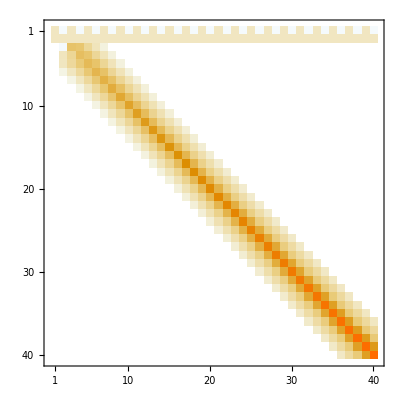

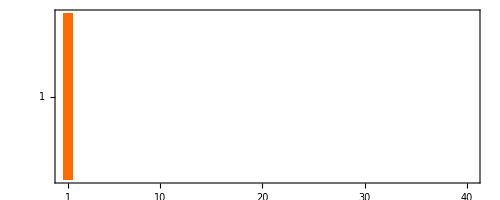

```mathematica
A[[2]]//MatrixPlot
{A[[1]]}//MatrixPlot
```

## Solve and post-process

```mathematica
solution=LinearSolve[A[[2]],A[[1]]]
```

{0.551528,-0.501361,-0.0515023,0.00136068,-0.0000259051,4.34215×10^-7,-6.79769×10^-9,1.01972×10^-10,-1.4856×10^-12,2.11878×10^-14,-2.9733×10^-16,4.11968×10^-18,-5.64974×10^-20,7.683×10^-22,-1.0379×10^-23,1.40373×10^-25,-2.098×10^-27,7.5096×10^-29,-1.10729×10^-29,2.32072×10^-30,-5.04202×10^-31,1.1067×10^-31,-2.44823×10^-32,5.45407×10^-33,-1.2228×10^-33,2.7575×10^-34,-6.25163×10^-35,1.42431×10^-35,-3.25976×10^-36,7.49192×10^-37,-1.72861×10^-37,4.00293×10^-38,-9.30112×10^-39,2.16807×10^-39,-5.06879×10^-40,1.18837×10^-40,-2.79342×10^-41,6.58082×10^-42,-1.54732×10^-42,3.40865×10^-43}

```mathematica
(* extract components from solution *)
ClearAll[out,outnull]
Block[{list,coef,assoc=<||>},
Table[
list[layer]=Sprouts`layout⟦layer⟧;
coef[layer]=Chop@GetComponent[solution,list[layer],layer,Sprouts`layout⟦layer⟧,Sprouts`nr];
AppendTo[assoc,AssociationThread[list[layer],coef[layer]]]
,{layer,1,Sprouts`nlayers}];
out=assoc;
]
outnull=Map[(#)->ConstantArray[0,Sprouts`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ-1,𝓂]]~Join~Map[(#)->ConstantArray[0,Sprouts`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ+1,𝓂]];
AppendTo[out,outnull];
```

```mathematica
ClearAll[NChebevalC]
NChebevalC[c_][x_]:=NChebeval[N[Re[c]]][x]+ⅈ NChebeval[N[Im[c]]][x]
xk=Cos[((2Range[1,Sprouts`nr]-1)π)/(2Sprouts`nr)]//N;
rk=Sprouts`rfu[1][xk];
```

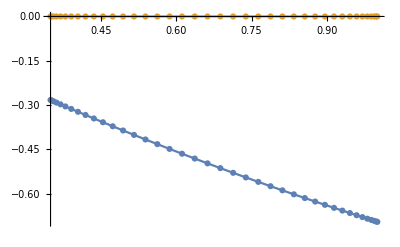

```mathematica
(* plot chosen component *)
data=NChebevalC[S[0,0]/.out]'[xk];
interp=Interpolation[{rk,data}ᵀ];
Show[Plot[{Re[interp[r]],Im[interp[r]]},{r,Min[rk],1},PlotRange->{{Min[rk],1},All}],ListPlot[{{rk,Re[data]}ᵀ,{rk,Im[data]}ᵀ}]]
```